## Deletion contraction illustrations

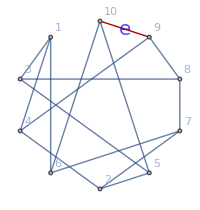

```mathematica
g=Graph[EdgeList[GraphData["PetersenGraph"]], VertexLabels->"Name", GraphHighlight->{UndirectedEdge[9, 10]},GraphLayout->"CircularEmbedding", ImageSize->200, EdgeLabels->{UndirectedEdge[9, 10]->Style["e",Blue,20]}]
```

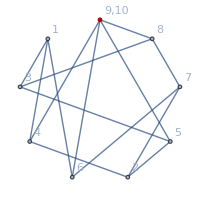

```mathematica
gContract=Graph[EdgeList[EdgeContract[g,UndirectedEdge[9, 10]]],VertexLabels->Join[Table[k->k,{k,1,8}],{9->"9,10"}],GraphLayout->"CircularEmbedding", GraphHighlight->{9}, ImageSize->200]
```

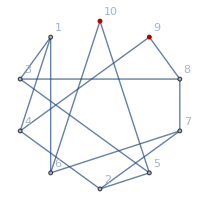

```mathematica
gDelete=Graph[EdgeList[EdgeDelete[g,UndirectedEdge[9, 10]]],VertexLabels->"Name",GraphLayout->"CircularEmbedding",GraphHighlight->{9,10}, ImageSize->200]
```

## Planar contraction illustrations

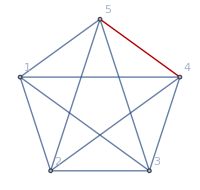

```mathematica
g=CompleteGraph[5,VertexLabels->"Name", GraphLayout->"CircularEmbedding", ImageSize->200,GraphHighlight->{UndirectedEdge[4,5]}]
```

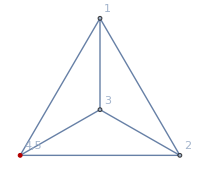

```mathematica
gContract=Graph[EdgeList[EdgeContract[g,UndirectedEdge[4,5]]],VertexLabels->Join[Table[k->k,{k,1,3}],{4->"4,5"}],GraphLayout->"TutteEmbedding", GraphHighlight->{4}, ImageSize->200]
```

## Examples of the complete base

```mathematica
Select[Keys[allGraphs5],EdgeCount[allGraphs5[#,"graph"]]==7&]
```

{29511,29493,29487,29485,29439,29433,29431,29415,29413,29407,29277,29271,29269,29253,29251,29245,29199,29197,29191,29173,28791,28785,28783,28767,28765,28759,28713,28711,28705,28687,28551,28549,28543,28525,28471,27333,27327,27325,27309,27307,27301,27255,27253,27247,27229,27093,27091,27085,27067,27013,26607,26605,26599,26581,26527,26365,22959,22953,22951,22935,22933,22927,22881,22879,22873,22855,22719,22717,22711,22693,22639,22233,22231,22225,22207,22153,21991,20775,20773,20767,20749,20695,20533,20047,9837,9831,9829,9813,9811,9805,9759,9757,9751,9733,9597,9595,9589,9571,9517,9111,9109,9103,9085,9031,8869,7653,7651,7645,7627,7573,7411,6925,3279,3277,3271,3253,3199,3037,2551,1093}

```mathematica
rep5=Table[allGraphs5[k,"colofour"]->Labeled[allGraphs5[k,"graph"],Style[SymbolToLabel[ allGraphs5[k,"colofour"]],ColourForKey[allGraphs5,k]]],{k,allGraphs5AtomKeys}];
```

```mathematica
With[{
k=29511},
allGraphs5[k,"graph"]
]
```

-Graphics-

```mathematica
allGraphs5[29511,"colofour"]/.rep5
```

-Graphics-1♁2♁345+-Graphics-1♁2♁34♁5+-Graphics-1♁2♁3♁45+-Graphics-1♁2♁35♁4+-Graphics-1♁2♁3♁4♁5